## Lattice Interpretation

```mathematica
bqfs={{5,0,1},{15,-10,2},{5,1,1},{5,-1,1},{5,2,1},{5,-2,1},{10,8,2},{10,-8,2},{5,3,1},{5,-3,1},{5,4,1},{5,-4,1}}
bqf2root[bqf_]:=Last[SolveValues[bqf.{x^2,x,1}==0,x]]
taus= Map[bqf2root,bqfs]
```

The picture illustrates an involution X_0(5) - > X_0(5) called the Fricke involution

On the upper half plane model, this involution is given by tau -> -5/tau

Upon applying this involution, there are precisely 10 points on the fundamental domain of X_0(5) whose image in X(1) stays the same after applying the Fricke involution. I will refer to these 10 points as the diagonal of X_0(5). Explicitly, those points are given by the following binary quadratic forms/taus:

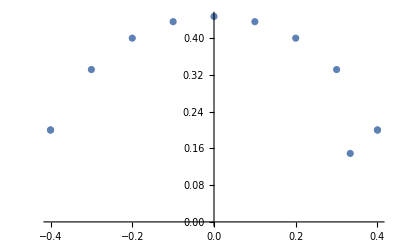

{{5,0,1},{15,-10,2},{5,1,1},{5,-1,1},{5,2,1},{5,-2,1},{10,8,2},{10,-8,2},{5,3,1},{5,-3,1},{5,4,1},{5,-4,1}}

{ⅈ/(√5),1/15 (5+ⅈ √5),1/10 (-1+ⅈ √19),1/10 (1+ⅈ √19),-1/5+(2 ⅈ)/5,1/5+(2 ⅈ)/5,-2/5+ⅈ/5,2/5+ⅈ/5,1/10 (-3+ⅈ √11),1/10 (3+ⅈ √11),-2/5+ⅈ/5,2/5+ⅈ/5}

```mathematica
ListPlot[Map[ReIm,taus]]
```

The point is that each of these taus gives rise to a lattice which contains a superlattice of index 5 which is homothetic to the original

The original lattice has basis 1, tau; the superlattice of index 5 will have basis 1/5, tau

It’s clear that 1/5, tau will generate a superlattice of index 5, the special thing about these taus is that the superlattice is homothetic to the original.

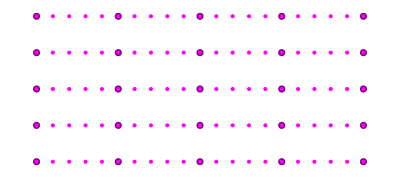

```mathematica
Show[ListPlot[Flatten[Table[a*{1,0}+b*ReIm[taus[[1]]],{a,-2,2},{b,-2,2}],1],PlotStyle->Purple],ListPlot[Flatten[Table[a*{1/5,0}+b*ReIm[taus[[1]]],{a,-10,10},{b,-10,10}],1],PlotStyle->Magenta],AspectRatio->True,Axes->False]
```

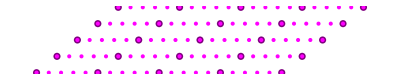

```mathematica
Show[ListPlot[Flatten[Table[a*{1,0}+b*ReIm[taus[[2]]],{a,-2,2},{b,-2,2}],1],PlotStyle->Purple],ListPlot[Flatten[Table[a*{1/5,0}+b*ReIm[taus[[2]]],{a,-10,10},{b,-10,10}],1],PlotStyle->Magenta],AspectRatio->True,Axes->False]
```

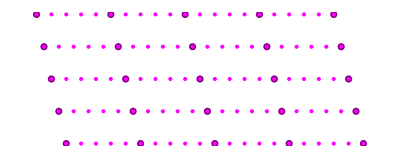

```mathematica
Show[ListPlot[Flatten[Table[a*{1,0}+b*ReIm[taus[[3]]],{a,-2,2},{b,-2,2}],1],PlotStyle->Purple],ListPlot[Flatten[Table[a*{1/5,0}+b*ReIm[taus[[3]]],{a,-10,10},{b,-10,10}],1],PlotStyle->Magenta],AspectRatio->True,Axes->False]
```

## Algebraic interpretation

We can reproduce this whole story algebraically

### Constructing X_0(5) algebraically

Need lots of formulae

```mathematica
ellcurve[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:=y^2+a1*x*y+a3*y-(x^3+a2*x^2+a4*x+a6)
lam[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=If[x1==x2,(a4+2 a2 x1+3 x1^2-a1*y1)/(2y1+a1*x1+a3),(y2-y1)/(x2-x1)]
nu[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=If[x1==x2,(-x1^3+a4*x1+2a6-a3*y1)/(2y1+a1*x1+a3),(y1*x2-y2*x1)/(x2-x1)]
x3[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=lam[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]^2+a1*lam[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]-a2-x1-x2
y3[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=-(lam[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]+a1)*x3[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]-nu[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]-a3
ellcurveplus[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:={x3[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}],y3[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]}
aineg[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:={x,-y-a1*x-a3}
ai2fg[{a1_,a2_,a3_,a4_,a6_}]:={-a1^4/48-(a1^2 a2)/6-a2^2/3+(a1 a3)/2+a4,a1^6/864+(a1^4 a2)/72+(a1^2 a2^2)/18+(2 a2^3)/27-(a1^3 a3)/24-(a1 a2 a3)/6+a3^2/4-(a1^2 a4)/12-(a2 a4)/3+a6}
fg2ai[{f_,g_}]:={0,0,0,f,g}
xyfg2xyai[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:={x+1/3 (-a1^2/4-a2),y-(a1*(x+1/3 (-a1^2/4-a2))+a3)/2}
xyai2xyfg[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:={a1^2/12+a2/3+x,1/2 (a3+a1 x+2 y)}
jfg[{f_,g_}]:=1728*(4f^3)/(4f^3+27g^2)
jai[ai_]:=Factor[jfg[ai2fg[ai]]]
uv2ai[{u_,v_}]:={1-u,-v,-v,0,0}
juv[{u_,v_}]:=jai[uv2ai[{u,v}]]
Fx[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:=a4+2 a2 x+3 x^2-a1 y
Fy[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:=-a3-a1 x-2 y
uQ[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:=(-a3-a1 x-2 y)^2
tQ[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:=2(a4+2 a2 x+3 x^2-a1 y)-a1(-a3-a1 x-2 y)
tS[{a1_,a2_,a3_,a4_,a6_},S_]:=Sum[tQ[{a1,a2,a3,a4,a6},S[[i]]],{i,1,Length[S]}]
wS[{a1_,a2_,a3_,a4_,a6_},S_]:=Sum[First[S[[i]]]*tQ[{a1,a2,a3,a4,a6},S[[i]]]+uQ[{a1,a2,a3,a4,a6},S[[i]]],{i,1,Length[S]}]
velu[{a1_,a2_,a3_,a4_,a6_},S_]:={a1,a2,a3,a4-5tS[{a1,a2,a3,a4,a6},S],a6-(a1^2+4a2)tS[{a1,a2,a3,a4,a6},S]-7wS[{a1,a2,a3,a4,a6},S]}
xIso[ai_,S_,x_]:=x+Sum[(tQ[ai,S[[i]]]/(x-S[[i]][[1]]))+(uQ[ai,S[[i]]]/(x-S[[i]][[1]])^2),{i,1,Length[S]}]
yIso[ai_,S_,{x_,y_}]:=y-Sum[(tQ[ai,S[[i]]]*(({x,y}-S[[i]]).{ai[[1]],1})/(x-S[[i]][[1]]))^2+((-Fy[ai,S[[i]]]*uQ[ai,S[[i]]]/(x-S[[i]][[1]])^3))+((ai[[1]]*uQ[ai,S[[i]]]-Fx[ai,S[[i]]]*Fy[ai,S[[i]]])/((x-S[[i]][[1]])^2)),{i,1,Length[S]}]
veluIso[ai_,S_,{x_,y_}]:={xIso[ai,S,x],yIso[ai,S,{x,y}]}
pP1[{u_,v_}]:={0,0}
nP1[{u_,v_}]:={0,v}
pP2[{u_,v_}]:={v,u*v}
nP2[{u_,v_}]:={v,0}
```

Step 1: Construct universal curve with a point of order 5 - I’ve done this before, here is the result:

```mathematica
ellcurve[uv2ai[uv5[t]],{x,y}]
```

t x^2-x^3-t y+(1-t) x y+y^2

If you replace t by a specific value, you obtain an elliptic curve with a point of order 5 at (0,0); and given any elliptic curve with a point of order 5, there is a unique equation of this form

Each point on this curve represents iso class of a pair (E, P), where P has order 5. The isomorphism type of the curve represented by a point on X_1(5) can be computed using:

```mathematica
j5x1[t_]:=juv[uv5[t]]
j5x1[t]
```

((1+12 t+14 t^2-12 t^3+t^4)^3)/(t^5 (-1-11 t+t^2))

We take a quotient by the involution that takes (E,P) to (E,2P) to obtain a model of X_0(5). I’m not going to bother working out the formula for (E,P)->(E,2P) - I will simply give the quotient map X_1(5)->X_0(5):

```mathematica
inv5[t_]:=-11+((t^2-1)/t)
```

The quotient map takes t in X_1(5) to inv5(t) in X_0(5). In X_0(5) coordinates, the map that takes a pair (E,P) to the j-invariant of E is given by j5x0[t], and the Fricke involution is given by t0->125/t0

```mathematica
j5x0[t_]:=((5+10 t+t^2)^3)/t
frx0v1[t_]:=125/t
```

```mathematica
Factor[j5x0[inv5[t]]]
```

((1+12 t+14 t^2-12 t^3+t^4)^3)/(t^5 (-1-11 t+t^2))

As you can see, the composition j5x0[quotient] is the same as j5x1

#### Algebraic pictures of X_0(5)

#### Application 1: j-invariants of associated lattices

The j-map can be computed explicitly on the algebraic side - we just need the algebraic coordinates on the points on the diagonal.

```mathematica
diagonalX05=FullSimplify[SolveValues[j5x0[t]==j5x0[125/t],t]]
```

{-11-2 ⅈ,-11+2 ⅈ,-2-11 ⅈ,-2+11 ⅈ,-5 √5,5 √5,-9-2 ⅈ √11,-9+2 ⅈ √11,7-2 ⅈ √19,7+2 ⅈ √19}

To obtain the j-invariants of the associated lattices, just plug these points into j5x0:

```mathematica
diagonal5jinvariants = FullSimplify[Map[j5x0,diagonalX05]]
```

{1728,1728,287496,287496,320 (1975-884 √5),320 (1975+884 √5),-32768,-32768,-884736,-884736}

This is a 10 element list, where some elements are repeated and others are irrational. It is easier to summarize this list by writing down a polynomial whose roots are the j-invariants, with the correct multiplicities:

```mathematica
Factor[Expand[Product[j-diagonal5jinvariants[[i]],{i,1,10}]]]
```

(-287496+j)^2 (-1728+j)^2 (32768+j)^2 (884736+j)^2 (-681472000-1264000 j+j^2)

Finally, we show that this polynomial will behave nicely when we reduce mod 5:

```mathematica
Factor[Expand[Product[j-diagonal5jinvariants[[i]],{i,1,10}]],Modulus->5]
```

j^2 (1+j)^2 (2+j)^2 (3+j)^2 (4+j)^2

## Application 2: Algebraic Lifts

We can use this set-up to obtain explicit formulae for algebraic lifts (E,phi) for each of the 10* isomorphism classes of elliptic curves mod 5.

### Getting the curves

Obtaining models of each E we need is easy - we simply lift the diagonal from X_0(5) to X_1(5).

Note that the map X_1(5) -> X_0(5) is a double cover, so there are two choices of points on X_1(5) for each point on the diagonal. It turns out that we can pick either of the two - the associated elliptic curves will be the same (one of the points represents (E,P), where P is a point in the kernel of the endomorphism of degree 5, and the other choice of points represents (E,2P).

To compute the coordinates of the lifts of the points on the diagonal of X_0(5) in X_1(5), we simply need to solve the equation quotient(t1) = t0 for t1 for each of the t0’s on the diagonal. This will require us to solve a quadratic polynomial, which is how we end up with two solutions. We can take either root of the quadratic to obtain an equation for the lift.

```mathematica
diagonalX15=First[Transpose[FullSimplify[Table[SolveValues[inv5[t]==diagonalX05[[i]],t],{i,1,10}]]]]
```

{-ⅈ,ⅈ,1/2 ((9-11 ⅈ)-3 √(-4-22 ⅈ)),1/2 ((9+11 ⅈ)-3 √(-4+22 ⅈ)),Root-1.09Root[1+22 #1-6 #1^2-22 #1^3+#1^4&,1]-1.0942270231806106,Root-0.0450Root[1+22 #1-6 #1^2-22 #1^3+#1^4&,2]-0.04499370036659311,Root-0.0441-0.140 ⅈRoot[1+4 #1+46 #1^2-4 #1^3+#1^4&,1]-0.044112036014083235,Root-0.0441+0.140 ⅈRoot[1+4 #1+46 #1^2-4 #1^3+#1^4&,2]-0.044112036014083235,Root18.0-8.70 ⅈRoot[1+36 #1+398 #1^2-36 #1^3+#1^4&,3]18.04497260878911,Root-0.0450+0.0217 ⅈRoot[1+36 #1+398 #1^2-36 #1^3+#1^4&,2]-0.044972608789109435}

To get equations for the curves, we use the universal curve with a point of order 5 lying above X_1(5)

```mathematica
Table[ellcurve[FullSimplify[uv2ai[uv5[diagonalX15[[i]]]]],{x,y}],{i,1,10}]
```

{-ⅈ x^2-x^3+ⅈ y+(1+ⅈ) x y+y^2,ⅈ x^2-x^3-ⅈ y+(1-ⅈ) x y+y^2,-1/2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)) x^2-x^3+1/2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)) y+1/2 ((-7+11 ⅈ)+3 √(-4-22 ⅈ)) x y+y^2,-1/2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)) x^2-x^3+1/2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)) y+1/2 ((-7-11 ⅈ)+3 √(-4+22 ⅈ)) x y+y^2,-x^3+y^2+x y Root2.09Root[-4+52 #1-66 #1^2+18 #1^3+#1^4&,4]2.094227023180611-x^2 Root1.09Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,4]1.0942270231806106+y Root1.09Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,4]1.0942270231806106,-x^3+y^2+x y Root1.04Root[-4+52 #1-66 #1^2+18 #1^3+#1^4&,3]1.044993700366593-x^2 Root0.0450Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,3]0.04499370036659311+y Root0.0450Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,3]0.04499370036659311,-x^3+y^2+x y Root1.04+0.140 ⅈRoot[48-88 #1+40 #1^2+#1^4&,4]1.0441120360140832-x^2 Root0.0441+0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,4]0.044112036014083235+y Root0.0441+0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,4]0.044112036014083235,-x^3+y^2+x y Root1.04-0.140 ⅈRoot[48-88 #1+40 #1^2+#1^4&,3]1.0441120360140832-x^2 Root0.0441-0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,3]0.044112036014083235+y Root0.0441-0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,3]0.044112036014083235,-x^3+y^2-x^2 Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911+y Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911+x y (1+Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911),-x^3+(-8-ⅈ √19+3 √(7+2 ⅈ √19)) x y+y^2-x^2 Root0.0450-0.0217 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,3]0.044972608789109435+y Root0.0450-0.0217 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,3]0.044972608789109435}

### Formulae for the endomorphisms

Finally, we obtain formulae for the lifts of Frobenius.

This part is a little bit trickier, and will be done in 2 steps:

First, we compute the quotient E -> E/<P>, where E is one of the curves above and <P> is the subgroup generated by the point of order 5 at (0,0).

The curve E/<P> will be isomorphic to the original curve E, but will initially be given by a different equation. We compute a change of variable E/<P> -> E, and then the formula for the endomorphism is obtained by composing the quotient E -> E/<P> and the change of variable E/<P> -> E.

#### Quotients

We can use Velu’s formulae to obtain a formula for E/<P> and a quotient map E-> E/<P>

```mathematica
originalequationsdomain =FullSimplify[ Map[uv2ai,Map[uv5,diagonalX15]]]
originalequationscodomain = FullSimplify[Map[velu5eq0,diagonalX15]]
```

{{1+ⅈ,ⅈ,ⅈ,0,0},{1-ⅈ,-ⅈ,-ⅈ,0,0},{1/2 ((-7+11 ⅈ)+3 √(-4-22 ⅈ)),1/2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)),1/2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)),0,0},{1/2 ((-7-11 ⅈ)+3 √(-4+22 ⅈ)),1/2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)),1/2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)),0,0},{Root2.09Root[-4+52 #1-66 #1^2+18 #1^3+#1^4&,4]2.094227023180611,Root1.09Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,4]1.0942270231806106,Root1.09Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,4]1.0942270231806106,0,0},{Root1.04Root[-4+52 #1-66 #1^2+18 #1^3+#1^4&,3]1.044993700366593,Root0.0450Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,3]0.04499370036659311,Root0.0450Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,3]0.04499370036659311,0,0},{Root1.04+0.140 ⅈRoot[48-88 #1+40 #1^2+#1^4&,4]1.0441120360140832,Root0.0441+0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,4]0.044112036014083235,Root0.0441+0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,4]0.044112036014083235,0,0},{Root1.04-0.140 ⅈRoot[48-88 #1+40 #1^2+#1^4&,3]1.0441120360140832,Root0.0441-0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,3]0.044112036014083235,Root0.0441-0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,3]0.044112036014083235,0,0},{1+Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911,Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911,Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911,0,0},{-8-ⅈ √19+3 √(7+2 ⅈ √19),Root0.0450-0.0217 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,3]0.044972608789109435,Root0.0450-0.0217 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,3]0.044972608789109435,0,0}}

{{1+ⅈ,ⅈ,ⅈ,10-10 ⅈ,5+5 ⅈ},{1-ⅈ,-ⅈ,-ⅈ,10+10 ⅈ,5-5 ⅈ},{1/2 ((-7+11 ⅈ)+3 √(-4-22 ⅈ)),1/2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)),1/2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)),55 ((118+80 ⅈ)-3 √(836+2098 ⅈ)),(542485/2-(703835 ⅈ)/2)-(187782-7293 ⅈ) √(-1-(11 ⅈ)/2)},{1/2 ((-7-11 ⅈ)+3 √(-4+22 ⅈ)),1/2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)),1/2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)),-55 ((-118+80 ⅈ)+3 √(836-2098 ⅈ)),(542485/2+(703835 ⅈ)/2)-(187782+7293 ⅈ) √(-1+(11 ⅈ)/2)},{Root2.09Root[-4+52 #1-66 #1^2+18 #1^3+#1^4&,4]2.094227023180611,Root1.09Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,4]1.0942270231806106,Root1.09Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,4]1.0942270231806106,-5 Root2.18Root[1936-41712 #1+44764 #1^2-11948 #1^3+#1^4&,3]2.178738697987424,Root-38.4Root[350579500+4653504500 #1+420935350 #1^2+7815590 #1^3+#1^4&,2]-38.37235573740609},{Root1.04Root[-4+52 #1-66 #1^2+18 #1^3+#1^4&,3]1.044993700366593,Root0.0450Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,3]0.04499370036659311,Root0.0450Root[1-22 #1-6 #1^2+22 #1^3+#1^4&,3]0.04499370036659311,5 Root-0.0490Root[1936+41712 #1+44764 #1^2+11948 #1^3+#1^4&,4]-0.048951479776866307,Root-0.0759Root[350579500+4653504500 #1+420935350 #1^2+7815590 #1^3+#1^4&,4]-0.07585642902585474},{Root1.04+0.140 ⅈRoot[48-88 #1+40 #1^2+#1^4&,4]1.0441120360140832,Root0.0441+0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,4]0.044112036014083235,Root0.0441+0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,4]0.044112036014083235,10 (82-11 ⅈ √11-30 √(6-2 ⅈ √11)),-11330-2735 ⅈ √11+√(46097339+61974242 ⅈ √11)},{Root1.04-0.140 ⅈRoot[48-88 #1+40 #1^2+#1^4&,3]1.0441120360140832,Root0.0441-0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,3]0.044112036014083235,Root0.0441-0.140 ⅈRoot[1-4 #1+46 #1^2+4 #1^3+#1^4&,3]0.044112036014083235,10 (82+11 ⅈ √11-30 √(6+2 ⅈ √11)),-11330+2735 ⅈ √11+√(46097339-61974242 ⅈ √11)},{1+Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911,Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911,Root-18.0+8.70 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911,10 (-566+485 ⅈ √19-30 √(-4610-610 ⅈ √19)),5 (237934+92989 ⅈ √19+3 √(-11964393533+4916721458 ⅈ √19))},{-8-ⅈ √19+3 √(7+2 ⅈ √19),Root0.0450-0.0217 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,3]0.044972608789109435,Root0.0450-0.0217 ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,3]0.044972608789109435,10 (-566-485 ⅈ √19+30 √(-4610+610 ⅈ √19)),5 Root-0.0137+0.0103 ⅈRoot[259346416+24171973336 #1+883618870328 #1^2-951736 #1^3+#1^4&,2]-0.013677827463186751}}

Verify that these equations represent the same curves:

```mathematica
FullSimplify[Map[jai,originalequationsdomain]]
FullSimplify[Map[jai,originalequationscodomain]]
```

{1728,1728,287496,287496,320 (1975-884 √5),320 (1975+884 √5),-32768,-32768,-884736,-884736}

{1728,1728,287496,287496,320 (1975-884 √5),320 (1975+884 √5),-32768,-32768,-884736,-884736}

#### Change of variable

First, we transform our equations so that all curves are given by an equation of the form y^2 = x^3 + fx + g - right now, the domain has the form y^2 + a1 xy + a3 y= x^3 and the codomain y^2 + a1 xy + a3 y = x^3 + a2x^2+a4 x + a6

```mathematica
fgsDom = FullSimplify[Map[ai2fg,originalequationsdomain]]
fgsCod = FullSimplify[Map[ai2fg,originalequationscodomain]]
```

{{1/4+ⅈ/2,0},{1/4-ⅈ/2,0},{-11/8 ((-61+217 ⅈ)+3 √(-4819-2942 ⅈ)),-7/16 ((-6300+2475 ⅈ)+√(33564379-31184978 ⅈ))},{11/8 ((61+217 ⅈ)-3 √(-4819+2942 ⅈ)),7/16 ((6300+2475 ⅈ)-(2511-1375 ⅈ) √(-1+(11 ⅈ)/2))},{-5/24 Root2.18Root[1936-41712 #1+44764 #1^2-11948 #1^3+#1^4&,3]2.178738697987424,1/108 (1289125-576505 √5+19 √(9206740250-4117379410 √5))},{5/24 Root-0.0490Root[1936+41712 #1+44764 #1^2+11948 #1^3+#1^4&,4]-0.048951479776866307,1/108 (1289125+576505 √5-19 √(9206740250+4117379410 √5))},{1/3 Root-0.0121+0.0958 ⅈRoot[400+1040 #1+42956 #1^2+404 #1^3+#1^4&,4]-0.01206435420369842,7/108 Root-0.0198-0.0291 ⅈRoot[15125+484000 #1+12237698 #1^2+6600 #1^3+#1^4&,3]-0.019775049461044778},{1/3 Root-0.0121-0.0958 ⅈRoot[400+1040 #1+42956 #1^2+404 #1^3+#1^4&,3]-0.01206435420369842,7/108 Root-0.0198+0.0291 ⅈRoot[15125+484000 #1+12237698 #1^2+6600 #1^3+#1^4&,4]-0.019775049461044778},{559+161 ⅈ √19+300 √(-2+2 ⅈ √19),1/4 Root-1.14 × 10^5+2.60 × 10^4 ⅈRoot[45125-38988000 #1+13722493234 #1^2+228456 #1^3+#1^4&,2]-114228.00142058729},{559-161 ⅈ √19-300 Root1.86-2.34 ⅈRoot[80+4 #1^2+#1^4&,3]1.8633668331811586,1/4 (-57114-2979 ⅈ √19+5 √(190 (651241+71639 ⅈ √19)))}}

{{41/4-(19 ⅈ)/2,0},{41/4+(19 ⅈ)/2,0},{11/8 ((4781+2983 ⅈ)-3 √(1551101+3169618 ⅈ)),-7/16 ((-628200+566775 ⅈ)+√(73401612899-712095892618 ⅈ))},{-11/8 ((-4781+2983 ⅈ)+3 √(1551101-3169618 ⅈ)),-7/16 ((-628200-566775 ⅈ)+√(73401612899+712095892618 ⅈ))},{-125/24 Root2.18Root[1936-41712 #1+44764 #1^2-11948 #1^3+#1^4&,3]2.178738697987424,-125/108 (1289125-576505 √5+19 √(9206740250-4117379410 √5))},{125/24 Root-0.0490Root[1936+41712 #1+44764 #1^2+11948 #1^3+#1^4&,4]-0.048951479776866307,125/108 (-1289125-576505 √5+19 √(9206740250+4117379410 √5))},{1/3 (2359-323 ⅈ √11-4 √(276454-95038 ⅈ √11)),7/108 (-130350-52925 ⅈ √11+√(22 (-628116767+627162149 ⅈ √11)))},{1/3 (2359+323 ⅈ √11-4 √(276454+95038 ⅈ √11)),7/108 (-130350+52925 ⅈ √11+√(22 (-628116767-627162149 ⅈ √11)))},{-5101+5011 ⅈ √19-600 √(-1253-142 ⅈ √19),1/4 (3126906+1518759 ⅈ √19+25 √(38 (-1433617211+399917221 ⅈ √19)))},{-5101-5011 ⅈ √19+600 √(-1253+142 ⅈ √19),1/4 (3126906-1518759 ⅈ √19-25 √(38 (-1433617211-399917221 ⅈ √19)))}}

Now, two pairs (f1,g1), (f2,g2)  represent isomorphic curves iff they have the same j invariant iff there exists t such that (f1 t^4, g1 t^6 ) = (f2, g2).

If both f, g are nonzero, we can obtain t^2 by computing t^6/t^4 = (g2/g1)/(f2/f1). We then compute a square root of that ratio to obtain t.

```mathematica
getsquareroot[z_]:=First[SolveValues[MinimalPolynomial[z,x^2]==0,x]]
fratios = FullSimplify[First[Transpose[fgsCod]]/First[Transpose[fgsDom]]]
fratiosNZg = Drop[fratios,2]
gratiosNZg = FullSimplify[Drop[Last[Transpose[fgsCod]],2]/Drop[Last[Transpose[fgsDom]],2]]
t2sNZg = FullSimplify[gratiosNZg/fratiosNZg]
tsNZg = FullSimplify[Map[getsquareroot,t2sNZg]]
tsAll = Join[{-1-2I,-1+2I},tsNZg]
```

{-7-24 ⅈ,-7+24 ⅈ,-7+24 ⅈ,-7-24 ⅈ,25,25,1/2 (-49+3 ⅈ √11),1/2 (-49-3 ⅈ √11),1/2 (31+9 ⅈ √19),1/2 (31-9 ⅈ √19)}

{-7+24 ⅈ,-7-24 ⅈ,25,25,1/2 (-49+3 ⅈ √11),1/2 (-49-3 ⅈ √11),1/2 (31+9 ⅈ √19),1/2 (31-9 ⅈ √19)}

{117-44 ⅈ,117+44 ⅈ,-125,-125,37+36 ⅈ √11,37-36 ⅈ √11,-27-28 ⅈ √19,-27+28 ⅈ √19}

{-3-4 ⅈ,-3+4 ⅈ,-5,-5,1/2 (-1-3 ⅈ √11),1/2 (-1+3 ⅈ √11),-1/2 ⅈ (-9 ⅈ+√19),1/2 ⅈ (9 ⅈ+√19)}

{-1-2 ⅈ,-1-2 ⅈ,-ⅈ √5,-ⅈ √5,-1/2 ⅈ (-3 ⅈ+√11),-1/2 ⅈ (-3 ⅈ+√11),-1/2 ⅈ (-ⅈ+√19),-1/2 ⅈ (-ⅈ+√19)}

```mathematica
tsAllcorrect={-1-2 ⅈ,-1+2 ⅈ,-1+2 ⅈ,-1-2 ⅈ,-ⅈ √5,-ⅈ √5,-3/2+(ⅈ √11)/2,-3/2-(ⅈ √11)/2,-1/2+(ⅈ √19)/2,-1/2-(ⅈ √19)/2}
```

{-1-2 ⅈ,-1+2 ⅈ,-1+2 ⅈ,-1-2 ⅈ,-ⅈ √5,-ⅈ √5,-3/2+(ⅈ √11)/2,-3/2-(ⅈ √11)/2,-1/2+(ⅈ √19)/2,-1/2-(ⅈ √19)/2}

```mathematica
FullSimplify[tsAllcorrect^4-fratios]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[tsAll^4-fratios]
```

{0,0,-48 ⅈ,0,0,0,-3 ⅈ √11,0,-9 ⅈ √19,0}

```mathematica
FullSimplify[fgsDom*Transpose[{tsAllcorrect^4,tsAllcorrect^6}]-fgsCod]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
ellcurve[originalequationsdomain[[1]],{x0,y0}]
ellcurve[originalequationscodomain[[1]],{x1,y1}]
```

-ⅈ x0^2-x0^3+ⅈ y0+(1+ⅈ) x0 y0+y0^2

(-5-5 ⅈ)-(10-10 ⅈ) x1-ⅈ x1^2-x1^3+ⅈ y1+(1+ⅈ) x1 y1+y1^2

I have a point (x1,y1) on the second model; want coordinates so it lives on the first model

```mathematica
ellcurve[originalequationscodomain[[1]],xyfg2xyai[originalequationscodomain[[1]],{x2,y2}]]
```

(-5-5 ⅈ)-(10-10 ⅈ) (-ⅈ/2+x2)-ⅈ (-ⅈ/2+x2)^2-(-ⅈ/2+x2)^3+ⅈ (1/2 (-ⅈ-(1+ⅈ) (-ⅈ/2+x2))+y2)+(1+ⅈ) (-ⅈ/2+x2) (1/2 (-ⅈ-(1+ⅈ) (-ⅈ/2+x2))+y2)+(1/2 (-ⅈ-(1+ⅈ) (-ⅈ/2+x2))+y2)^2

```mathematica
Clear[y3]
```

```mathematica
Expand[%]
```

(-41/4+(19 ⅈ)/2) x2-x2^3+y2^2

(x2,y2) live on the simple curve above; when we plug them into xyfg2xyai we get solutions of the x1,y1 equation

Next, we rescale x2, y2

```mathematica
removelc[poly_,x_]:=Expand[poly/Last[CoefficientList[poly,x]]]
Expand[removelc[ellcurve[originalequationscodomain[[1]],xyfg2xyai[originalequationscodomain[[1]],{tsAll[[1]]^(2)x3,tsAll[[1]]^(3)y3}]],x3]]
```

(1/4+ⅈ/2) x3+x3^3-y3^2

Finally, we need to undo the analog of the (x0,y0)->(x1,y1) step for the equation we want to work with.

```mathematica
xy3toxy0[{x3_,y3_},i_]:=xyfg2xyai[originalequationscodomain[[i]],{tsAll[[i]]^(2)x3,tsAll[[i]]^(3)y3}]
xy4toxy0[{x4_,y4_},i_]:=
xy3toxy0[xyai2xyfg[originalequationsdomain[[i]],{x4,y4}],i]
```

```mathematica
xy4toxy3ex[{x4_,y4_}]:={ⅈ/2+x4,1/2 (ⅈ+(1+ⅈ) x4+2 y4)}
xy4toxy0ex[{x4_,y4_}]:=xy3toxy0[xyai2xyfg[originalequationsdomain[[1]],{x4,y4}],1]
```

```mathematica
FullSimplify[xy4toxy0ex[{x4,y4}]]
```

{(-2-2 ⅈ)-(3-4 ⅈ) x4,(-1+7 ⅈ)+(8+6 ⅈ) x4+(11+2 ⅈ) y4}

```mathematica
FullSimplify[xy4toxy0[{x4,y4},1]]
```

{(-2-2 ⅈ)-(3-4 ⅈ) x4,(-1+7 ⅈ)+(8+6 ⅈ) x4+(11+2 ⅈ) y4}

```mathematica
ellcurve[originalequationsdomain[[1]],{x4,y4}]
ellcurve[originalequationscodomain[[1]],{x4,y4}]
```

-ⅈ x4^2-x4^3+ⅈ y4+(1+ⅈ) x4 y4+y4^2

(-5-5 ⅈ)-(10-10 ⅈ) x4-ⅈ x4^2-x4^3+ⅈ y4+(1+ⅈ) x4 y4+y4^2

```mathematica
removelc[ellcurve[originalequationscodomain[[1]],xy4toxy0ex[{x4,y4}]],x4]
```

ⅈ x4^2+x4^3-ⅈ y4-(1+ⅈ) x4 y4-y4^2

If (x4, y4) satisfy the desired equation, then their images under the xy4toxy0 map will satisfy the given equation. We need the inverse of this map:

```mathematica
First[SolveValues[xy4toxy0ex[{x4,y4}]=={x0,y0},{x4,y4}]]
```

{(-3/25-(4 ⅈ)/25) ((2+2 ⅈ)+x0),(2/125+(11 ⅈ)/125) ((-3+3 ⅈ)+2 x0-ⅈ y0)}

```mathematica
xy0toxy4ex[{x0_,y0_}]:={(-3/25-(4 ⅈ)/25) ((2+2 ⅈ)+x0),(2/125+(11 ⅈ)/125) ((-3+3 ⅈ)+2 x0-ⅈ y0)}
```

```mathematica
xy4toxy0[{x4_,y4_},i_]:=
xy3toxy0[xyai2xyfg[originalequationsdomain[[i]],{x4,y4}],i]
```

```mathematica
xy0toxy4[{x0_,y0_},i_]:=First[SolveValues[xy4toxy0[{x4,y4},i]=={x0,y0},{x4,y4}]]
```

```mathematica
FullSimplify[Table[xy0toxy4[{x0,y0},i],{i,1,10}]]
```

```mathematica
chvarsall[{x0_,y0_}]:={{(-3/25-(4 ⅈ)/25) ((2+2 ⅈ)+x0),(2/125+(11 ⅈ)/125) ((-3+3 ⅈ)+2 x0-ⅈ y0)},{(-3/25+(4 ⅈ)/25) ((2-2 ⅈ)+x0),(11/125+(2 ⅈ)/125) ((-3+3 ⅈ)-2 ⅈ x0+y0)},{(-3/25-(4 ⅈ)/25) ((-37-7 ⅈ)+√(1364+502 ⅈ)+x0),1/250 √(44+117 ⅈ) ((-329-135 ⅈ) √(-2-11 ⅈ)+(744-393 ⅈ) √2+6 √(-2-11 ⅈ) x0-(7-11 ⅈ) √2 x0-2 (-1)^(3/4) y0)},{(3/25+(4 ⅈ)/25) ((-7-37 ⅈ)+√(-1364+502 ⅈ)-x0),1/250 (((8-206 ⅈ)+30 √(-55+10 ⅈ)) x0+(7+ⅈ) ((1903+24 ⅈ)-5 √(144595+3610 ⅈ)+(3-ⅈ) y0))},{1/10 (-92+40 √5-5 √(650-290 √5)-2 x0),1/200 ((-18590-50 ⅈ)+(8350+22 ⅈ) √5+100 √(4450-1990 √5)+5 √(50-22 √5) ((-475-2 ⅈ)+207 √5)+2 ((-45-25 ⅈ)+(25+9 ⅈ) √5+5 √(50-22 √5) (-ⅈ+√5)) x0-8 ⅈ √5 y0)},{-46/5-4 √5+√(5/2 (65+29 √5))-x0/5,1/200 ((-18590+50 ⅈ)-(8350-22 ⅈ) √5+(2375-10 ⅈ) √(50+22 √5)+1035 √(250+110 √5)-100 √(4450+1990 √5)+2 ((-45+25 ⅈ)-(25-9 ⅈ) √5+5 (-ⅈ+√5) √(50+22 √5)) x0-8 ⅈ √5 y0)},{-(4 ⅈ x0+(ⅈ+√11) Root"0.623"+"0.427" ⅈRoot[368-776 #1+584 #1^2+48 #1^3+#1^4&,4]0.6234919557245377)/(2 ⅈ+6 √11),1/(-114 ⅈ+58 √11)(2 √(-1337073+422169 ⅈ √11+5 √(-6909850370-45157730890 ⅈ √11))-19 √(20+2 ⅈ √11-2 √(99+22 ⅈ √11)) x0+7 √(22 (-10-ⅈ √11+√(99+22 ⅈ √11))) x0+(2 ⅈ+6 √11) y0)},{(-4 ⅈ x0+(ⅈ+√11) Root"-0.623"+"0.427" ⅈRoot[368+776 #1+584 #1^2-48 #1^3+#1^4&,2]-0.6234919557245377)/(2 ⅈ+6 √11),1/(-57 ⅈ+29 √11)(√(2 (-679982+184121 ⅈ √11+√(89496249611-250402829858 ⅈ √11)))+√(-2353-1241 ⅈ √11+√(22 (-579547+293191 ⅈ √11))) x0+(ⅈ+3 √11) y0)},{-(37 ⅈ+67 √19+√(83698+4622 ⅈ √19)+4 ⅈ x0)/(2 (9 ⅈ+√19)),1/(-2424 ⅈ+264 √19)(-24 (9 ⅈ+√19) y0+6 (-23 ⅈ+3 √19) (7+537 ⅈ √19+√(-5479138+6718 ⅈ √19)+2 x0 (1+Root"-18.0"+"8.70" ⅈRoot[1-36 #1+398 #1^2+36 #1^3+#1^4&,2]-18.04497260878911)))},{-(√(-7837-9743 ⅈ √19+25 √(-2787682+244318 ⅈ √19))+2 ⅈ x0)/(9 ⅈ+√19),1/(√(29122-31358 ⅈ √19))(√(-1903639493+1149534127 ⅈ √19+5 √(-859332166136025698-175063904507594878 ⅈ √19))+√(345569-22141 ⅈ √19-3 √(2 (6112952779-830642581 ⅈ √19))) x0-(1+ⅈ) √(559 ⅈ+√19) y0)}}
```

```mathematica
Factor[Table[chvarsall[velu5iso0[diagonalX15[[i]],{x,y}]][[i]],{i,1,10}]]
```

```mathematica
endomorphisms[{x_,y_}]:={5^2,5^3}*
```

We’re not going to check everything, but let’s look at the x coords of first 4 terms

```mathematica
endosx1tox4[x_]:=25{-((3/25+(4 ⅈ)/25) (1+(1-3 ⅈ) x-(5+5 ⅈ) x^2-(7-6 ⅈ) x^3+(2+4 ⅈ) x^4+x^5))/(x^2 (ⅈ+x)^2),((4/25+(3 ⅈ)/25) (ⅈ-(3-ⅈ) x-(5+5 ⅈ) x^2+(6-7 ⅈ) x^3+(4+2 ⅈ) x^4+ⅈ x^5))/(x^2 (-ⅈ+x)^2),-(((6/25+(8 ⅈ)/25) ((-37762+15048 ⅈ)+(7560+4092 ⅈ) √(-4-22 ⅈ)-(30229-19173 ⅈ) x+(7209+2310 ⅈ) √(-4-22 ⅈ) x+(7439+11123 ⅈ) x^2+(798-2715 ⅈ) √(-4-22 ⅈ) x^2-(54-66 ⅈ) √(-2-11 ⅈ) √(682+251 ⅈ) x^2-(38+198 ⅈ) √(1364+502 ⅈ) x^2-(1814+2646 ⅈ) x^3-(183-651 ⅈ) √(-4-22 ⅈ) x^3+12 √(-2-11 ⅈ) √(682+251 ⅈ) x^3-(18-22 ⅈ) √(1364+502 ⅈ) x^3-(92-8 ⅈ) x^4+6 √(-4-22 ⅈ) x^4+2 √(1364+502 ⅈ) x^4+2 x^5))/(x^2 ((-9+11 ⅈ)+3 √(-4-22 ⅈ)+2 x)^2)),-(((6/25+(8 ⅈ)/25) ((-37762-15048 ⅈ)+(7560-4092 ⅈ) √(-4+22 ⅈ)-(30229+19173 ⅈ) x+(7209-2310 ⅈ) √(-4+22 ⅈ) x-(173+3551 ⅈ) x^2+(38-198 ⅈ) √(-1364+502 ⅈ) x^2+(600+453 ⅈ) √(-4+22 ⅈ) x^2+(54+66 ⅈ) √(-682+251 ⅈ) √(-2+11 ⅈ) x^2-(1946-1138 ⅈ) x^3+(18+22 ⅈ) √(-1364+502 ⅈ) x^3+(81-471 ⅈ) √(-4+22 ⅈ) x^3-12 √(-682+251 ⅈ) √(-2+11 ⅈ) x^3-(4-52 ⅈ) x^4-2 √(-1364+502 ⅈ) x^4+6 √(-4+22 ⅈ) x^4+2 x^5))/(x^2 ((-9-11 ⅈ)+3 √(-4+22 ⅈ)+2 x)^2))}
```

Actually lets not. This just gets messy.

The graph interpretation is next.